# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP
∅ → T
T → ∅ 

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP] + k[11]k_d-k_d[T],
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=5;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t]+k11[t]*kd-kd*x[7][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,2.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=1;totP=1;totS=1;
stepNum=5;
sampleSize=100000;

pars={};
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=2.*10^(RandomReal[]*4-3);

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*Min[(0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.0001]),1.0])];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,10];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
(*Export["saturationSampling.csv",transPars];*)
Export["unsaturationSampling.csv",transPars];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 5171.72 and t = 5224.49.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 102.768 and t = 103.467.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 175.346 and t = 176.181.

General::stop: Further output of NDSolve :: evcvmit will be suppressed during this calculation.

{26821.2,Null}

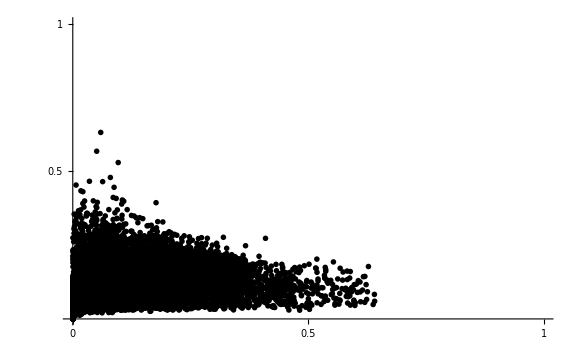

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[15]]]
```

{0.641223,98236}

```mathematica
maxAndIndex[transPars[[16]]]
```

{0.631595,31386}

```mathematica
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
pars[[usIndex]]
```

{0.18691,0.11489,956.486,0.00117357,1.19166,0.306976,122.133,0.00565569,0.706665,0.25641,3.62406,1,1,1,0.641223,0.0599328,98236,5117.98,1276.99,0.0000463075,0.362845}

```mathematica
pars[[adIndex]]
```

{328.589,0.00116038,240.675,54.1912,0.325441,58.5094,0.201854,0.00123987,10.9987,0.327257,0.0116813,1,1,1,0.0593904,0.631595,31386,0.732454,1.08569,0.00614243,0.0297541}

{a→0.974489,b→0.250516,hillK→945.506,n→1.82381}

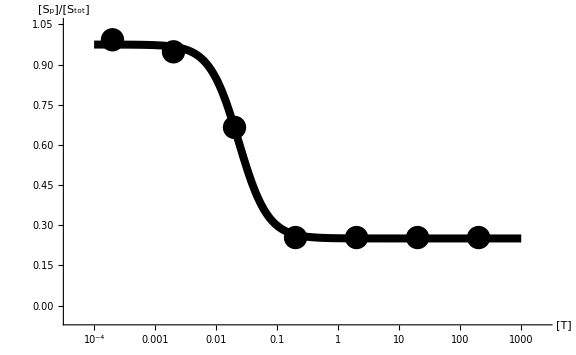

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,2.*10^-4};
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
stepNum=6;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];totT=pars[[usIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10^3},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[T]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}], PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 4644.4 and t = 4701.24.

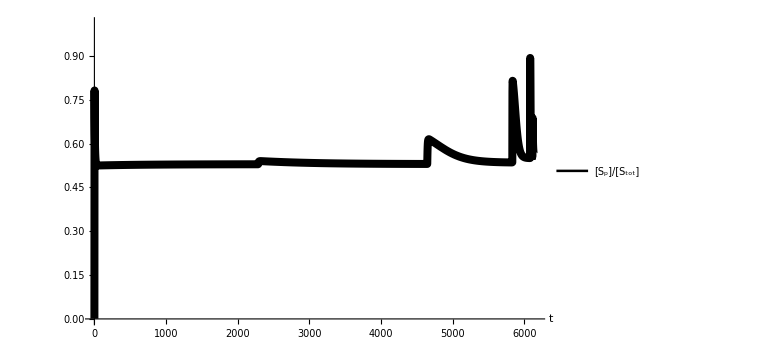

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,2.*10^-4};
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

0.0116813

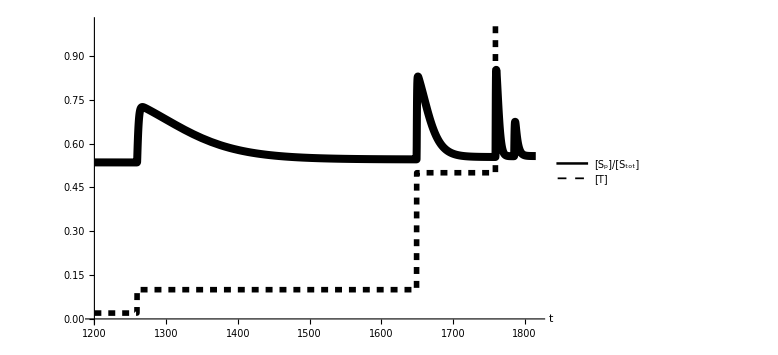

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.02};
stepNum=4;
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]]
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,1200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.25,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,1200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[T]"},{0.55,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

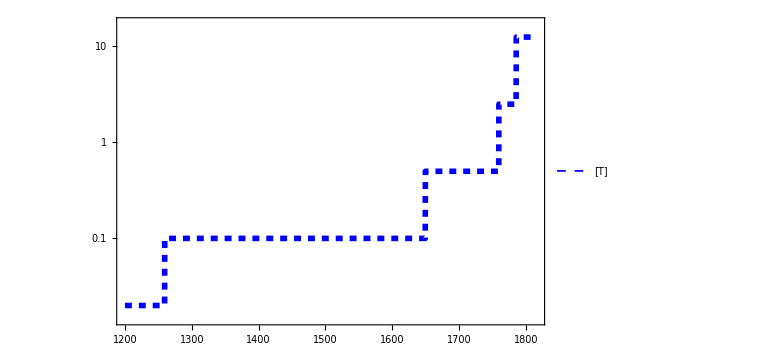

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,1200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[T]"},{0.15,0.9}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

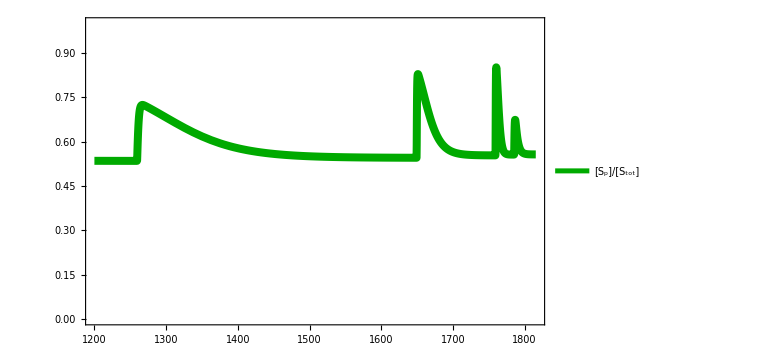

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,1200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.55,0.9}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{input,output}]
Export["scaffoldTitrationAlternativeUnsaturatedAd.eps",adPlot];
Export["scaffoldTitrationAlternativeUnsaturatedAd.pdf",adPlot];
```

-Graphics--Graphics-